```mathematica
SubPlus[ψ][x_]:=Subscript[A, n] Exp[I k x] + Subscript[B, n] Exp[-I k x]
SubMinus[ψ][x_]:=Subscript[A, n+1] Exp[I k x] +Subscript[B, n+1] Exp[-I k x]
Subscript[V, n_][y_]:=α*Subscript[δ, x][y-Subscript[x, n]]
Subscript[X, n_]:=n a
" "
H[t_]:=Solve[{D[SubMinus[ψ][Subscript[x, n]],Subscript[x, n]]  -  D[SubPlus[ψ][Subscript[x, n]],Subscript[x, n]]==(2m)/ℏ^2 α SubPlus[ψ][Subscript[x, n]]&&SubMinus[ψ][Subscript[x, n]]==SubPlus[ψ][Subscript[x, n]], β==(m α)/(ℏ^2 k)},{Subscript[A, n+1],Subscript[B, n+1]},{α,m,ℏ}][[1]]/.n->t
```

### Firstly, let’s see the potential that we are dealing with:

```mathematica
Manipulate[Plot[∑_(l=1)^n (1.*^3)/(π*((s-Subscript[X, 10l])^2+(1.*^-3)^2))/.a->1,{s,-020,120},PlotRange->Automatic,PlotStyle->{AbsoluteThickness[3.],Black}],{n,0,10,1}]
```

### Starting from T.I. Schrodinger’s Equation

```mathematica
Dt[Ψ[x],{x,2}]==(-2m)/ℏ^2(T-Subscript[V, n][x])Ψ[x]//TraditionalForm
Integrate[Dt[Ψ[x],{x,2}]==-(2m)/ℏ^2(T-Subscript[V, n][x])Ψ[x],{x,-ϵ,ϵ}]//TraditionalForm
Dt[Ψ[ϵ],{ϵ,1}]+Dt[Ψ[-ϵ],{ϵ,1}]==(2m)/ℏ^2 α Ψ[Subscript[x, n]]//TraditionalForm
Limit[Dt[Ψ[ϵ],{ϵ,1}]+Dt[Ψ[-ϵ],{ϵ,1}],ϵ->Subscript[x, n]]==SubPlus[Ψ][Subscript[x, n]]-SubMinus[Ψ][Subscript[x, n]]//TraditionalForm
SubPlus[Ψ]'[Subscript[x, n]]-SubMinus[Ψ]'[Subscript[x, n]]==(2m)/ℏ^2 α Ψ[Subscript[x, n]]//TraditionalForm
```

Ψ_+'(x_n)-Ψ_-'(x_n)==(2 α m Ψ(x_n))/ℏ^2

(Ψ'(ϵ)-Ψ'(-ϵ))ϵx_n==Ψ_+(x_n)-Ψ_-(x_n)

Ψ'(ϵ)-Ψ'(-ϵ)==(2 α m Ψ(x_n))/ℏ^2

∫_-ϵ^ϵ (Ψ''(x)==-(2 m Ψ(x) (T-α δ_x(x-x_n)))/ℏ^2)ⅆx

Ψ''(x)==-(2 m Ψ(x) (T-α δ_x(x-x_n)))/ℏ^2

Ψ''(x)==-(2 m Ψ(x) (T-α δ_x(x-x_n)))/ℏ^2
∫_-ϵ^ϵ (Ψ''(x)==-(2 m Ψ(x) (T-α δ_x(x-x_n)))/ℏ^2)ⅆx
Ψ'(ϵ)-Ψ'(-ϵ)==(2 α m Ψ(x_n))/ℏ^2
(Ψ'(ϵ)-Ψ'(-ϵ))ϵx_n==Ψ_+(x_n)-Ψ_-(x_n)
Ψ_+'(x_n)-Ψ_-'(x_n)==(2 α m Ψ(x_n))/ℏ^2

So we have two boundary conditions, The first is:

```mathematica
SubPlus[Ψ][Subscript[x, n]]==SubMinus[Ψ][Subscript[x, n]]//TraditionalForm
SubPlus[ψ][x]==SubMinus[ψ][x]//TraditionalForm
```

A_n ⅇ^(ⅈ k x)+B_n ⅇ^(-ⅈ k x)==A_(n+1) ⅇ^(ⅈ k x)+B_(n+1) ⅇ^(-ⅈ k x)

Ψ_+(x_n)==Ψ_-(x_n)

Ψ_+(x_n)==Ψ_-(x_n)
A_n ⅇ^(ⅈ k x)+B_n ⅇ^(-ⅈ k x)==A_(n+1) ⅇ^(ⅈ k x)+B_(n+1) ⅇ^(-ⅈ k x)

### The second:

```mathematica
SubPlus[Ψ]'[Subscript[x, n]]-SubMinus[Ψ]'[Subscript[x, n]]==(2m)/ℏ^2 Ψ[Subscript[x, n]]//TraditionalForm
D[SubMinus[Ψ][x],x]  -  D[SubPlus[Ψ][x],x]==(2m)/ℏ^2 α (SubPlus[ψ][Subscript[x, n]])/.x->Subscript[x, n]//TraditionalForm
D[SubPlus[ψ][x],x]==D[SubMinus[ψ][x],x]==(2m)/ℏ^2 α (SubPlus[ψ][Subscript[x, n]])/.x->Subscript[x, n]//TraditionalForm
```

Ψ_+'(x_n)-Ψ_-'(x_n)==(2 m Ψ(x_n))/ℏ^2

Ψ_-'(x_n)-Ψ_+'(x_n)==(2 α m (A_n ⅇ^(ⅈ k x_n_n)+B_n ⅇ^(-ⅈ k x_n_n)))/ℏ^2

ⅈ k A_n ⅇ^(ⅈ k x_n)-ⅈ k B_n ⅇ^(-ⅈ k x_n)==ⅈ k A_(n+1) ⅇ^(ⅈ k x_n)-ⅈ k B_(n+1) ⅇ^(-ⅈ k x_n)==(2 α m (A_n ⅇ^(ⅈ k x_n_n)+B_n ⅇ^(-ⅈ k x_n_n)))/ℏ^2

Calling β = (m α)/(ℏ^2 k), Then simplifying the last equation

```mathematica
D[SubMinus[ψ][x],x]  -  D[SubPlus[ψ][x],x]==(2m)/ℏ^2 α (SubPlus[ψ][Subscript[x, n]])/.x->Subscript[x, n]//TraditionalForm//Simplify
  ⅇ^(-ⅈ k Subscript[x, n]) (Subscript[A, n] (-ⅇ^(2 ⅈ k Subscript[x, n]))+Subscript[B, n]+F ⅇ^(2 ⅈ k Subscript[x, n])-G)==(2 α m (SubPlus[ψ][Subscript[x, n]]))/(ⅈ k ℏ^2)//TraditionalForm
  ⅇ^(-ⅈ k Subscript[x, n]) (Subscript[A, n] (-ⅇ^(2 ⅈ k Subscript[x, n]))+Subscript[B, n]+F ⅇ^(2 ⅈ k Subscript[x, n])-G)==-2ⅈ β (SubPlus[ψ][Subscript[x, n]])//TraditionalForm
```

-ⅈ k ⅇ^(-ⅈ k x_n) (A_n ⅇ^(2 ⅈ k x_n)-A_(n+1) ⅇ^(2 ⅈ k x_n)-B_n+B_(n+1))==(2 α m ⅇ^(-ⅈ k x_n_n) (B_n+A_n ⅇ^(2 ⅈ k x_n_n)))/ℏ^2

ⅇ^(-ⅈ k x_n) (-A_n ⅇ^(2 ⅈ k x_n)+B_n+F ⅇ^(2 ⅈ k x_n)-G)==-(2 ⅈ α m (A_n ⅇ^(ⅈ k x_n)+B_n ⅇ^(-ⅈ k x_n)))/(k ℏ^2)

ⅇ^(-ⅈ k x_n) (-A_n ⅇ^(2 ⅈ k x_n)+B_n+F ⅇ^(2 ⅈ k x_n)-G)==-2 ⅈ β (A_n ⅇ^(ⅈ k x_n)+B_n ⅇ^(-ⅈ k x_n))

Now we have these two equations that we will solve for A_(n+1) and B_(n+1) then construct the matrix M_n which is the coefficient matrix of A_n and B_n and represent the Transfer Matrix

```mathematica
SubMinus[ψ][Subscript[x, n]]==SubPlus[ψ][Subscript[x, n]]//TraditionalForm //TraditionalForm
 ⅇ^(-ⅈ k Subscript[x, n]) (Subscript[A, n] (-ⅇ^(2 ⅈ k Subscript[x, n]))+Subscript[B, n]+F ⅇ^(2 ⅈ k Subscript[x, n])-G)==-2ⅈ β (Subscript[A, n]+Subscript[B, n])//TraditionalForm
```

A_(n+1) ⅇ^(ⅈ k x_n)+B_(n+1) ⅇ^(-ⅈ k x_n)==A_n ⅇ^(ⅈ k x_n)+B_n ⅇ^(-ⅈ k x_n)

ⅇ^(-ⅈ k x_n) (-A_n ⅇ^(2 ⅈ k x_n)+B_n+F ⅇ^(2 ⅈ k x_n)-G)==-2 ⅈ β (A_n+B_n)

```mathematica
S = Solve[{D[SubMinus[ψ][Subscript[x, n]],Subscript[x, n]]  -  D[SubPlus[ψ][Subscript[x, n]],Subscript[x, n]]==(2m)/ℏ^2 α SubPlus[ψ][Subscript[x, n]]&&SubMinus[ψ][Subscript[x, n]]==SubPlus[ψ][Subscript[x, n]], β==(m α)/(ℏ^2 k)},{Subscript[A, n+1],Subscript[B, n+1]},{α,m,ℏ}][[1]];
S/.Rule->Equal//TraditionalForm
"M_n"==MatrixForm@Normal@CoefficientArrays[{Subscript[A, n+1]/. S,Subscript[B, n+1]/. S},{Subscript[A, n],Subscript[B, n]}][[2]]//TraditionalForm
```

{A_(n+1)==-ⅈ (β A_n+ⅈ A_n+β B_n ⅇ^(-2 ⅈ k x_n)),B_(n+1)==ⅈ β A_n ⅇ^(2 ⅈ k x_n)+ⅈ β B_n+B_n}

M_n==(1-ⅈ β | -ⅈ β ⅇ^(-2 ⅈ k x_n)
ⅈ β ⅇ^(2 ⅈ k x_n) | 1+ⅈ β)

Arranging the matrices yields

```mathematica
MatrixForm@{Subscript[A, n+1],Subscript[B, n+1]}=="M_n"MatrixForm@{Subscript[A, n],Subscript[B, n]}//TraditionalForm
MatrixForm@{Subscript[A, n+1],Subscript[B, n+1]} ==MatrixForm@Normal@CoefficientArrays[{Subscript[A, n+1]/. S,Subscript[B, n+1]/. S},{Subscript[A, n],Subscript[B, n]}][[2]]| MatrixForm@{Subscript[A, n],Subscript[B, n]}//MatrixForm//TraditionalForm
```

(A_(n+1)
B_(n+1))==M_n (A_n
B_n)

(A_(n+1)
B_(n+1))==(1-ⅈ β | -ⅈ ⅇ^(-2 ⅈ k x_n) β
ⅈ ⅇ^(2 ⅈ k x_n) β | ⅈ β+1)|(A_n
B_n)

Let’s Assume That we have three barriers, so n = 0, 1 , 2. We will now observe the behavior of the relationships between coefficients

```mathematica
MatrixForm@{Subscript[A, n+1],Subscript[B, n+1]}=="M_n"MatrixForm@{Subscript[A, n],Subscript[B, n]}//TraditionalForm
MatrixForm@{Subscript[A, n+1],Subscript[B, n+1]} ==Normal@CoefficientArrays[{Subscript[A, n+1]/. S,Subscript[B, n+1]/. S},{Subscript[A, n],Subscript[B, n]}][[2]]| MatrixForm@{Subscript[A, n],Subscript[B, n]}//MatrixForm//TraditionalForm
```

(A_(n+1)
B_(n+1))==M_n (A_n
B_n)

(A_(n+1)
B_(n+1))==(1-ⅈ β | -ⅈ β ⅇ^(-2 ⅈ k x_n)
ⅈ β ⅇ^(2 ⅈ k x_n) | 1+ⅈ β)|(A_n
B_n)

Setting n = 2, 1 ,0. Respectively, we get:

```mathematica
MatrixForm@{Subscript[A, n+1],Subscript[B, n+1]}==Subscript[M, n] MatrixForm@{Subscript[A, n],Subscript[B, n]}/.n->2//TraditionalForm
MatrixForm@{Subscript[A, n+1],Subscript[B, n+1]}==Subscript[M, n] MatrixForm@{Subscript[A, n],Subscript[B, n]}/.n->1//TraditionalForm
MatrixForm@{Subscript[A, n+1],Subscript[B, n+1]}==Subscript[M, n] MatrixForm@{Subscript[A, n],Subscript[B, n]}/.n->0//TraditionalForm
```

(A_3
B_3)==M_2 (A_2
B_2)

(A_2
B_2)==M_1 (A_1
B_1)

(A_1
B_1)==M_0 (A_0
B_0)

Combining them in one equation yields:

```mathematica
MatrixForm@{Subscript[A, n+1],Subscript[B, n+1]}==(∏_(l=0)^2 Subscript[M, l])MatrixForm@{Subscript[A, 0],Subscript[B, 0]}/.n->2//TraditionalForm
```

(A_3
B_3)==M_0 M_1 M_2 (A_0
B_0)

We can now generalize this for n = 0, 1 , 2 ..., N:

```mathematica
MatrixForm@{Subscript[A, N+1],Subscript[B, N+1]}==∏_(n=0)^N Subscript[M, n] MatrixForm@{Subscript[A, 0],Subscript[B, 0]}//TraditionalForm
```

(A_(N+1)
B_(N+1))==∏_(n=0)^N M_n (A_0
B_0)

Here you can Play with N to see the resultant matrix:

```mathematica
Manipulate[MatrixForm@{Subscript[A, N+1],Subscript[B, N+1]}==(∏_(n=0)^N Subscript[M, n])MatrixForm@{Subscript[A, 0],Subscript[B, 0]}//TraditionalForm,{N,0,10,1}]
```

Now let’s check the determinant of M_n and check if it yields unity

```mathematica
"M_n"==MatrixForm@Normal@CoefficientArrays[{Subscript[A, n+1]/. H[n],Subscript[B, n+1]/. H[n]},{Subscript[A, n],Subscript[B, n]}][[2]]//TraditionalForm
M[n_]:=Normal@CoefficientArrays[{Subscript[A, n+1]/. H[n],Subscript[B, n+1]/. H[n]},{Subscript[A, n],Subscript[B, n]}][[2]];
De[m_]:=Reverse@Table[M[n],{n,0,m,1}]
wq[qq_]:=ParallelCombine[Dot[Sequence@@##]&,De[qq]/.k->m/.β->1/m/.Subscript[x, n_]->n,Dot]
"M = ∏_(n = 0)^N  M_n"//TraditionalForm
( Det[ M]//HoldForm)==Det[wq[1]]//FullSimplify//TraditionalForm
```

M_n==(1-ⅈ β | -ⅈ β ⅇ^(-2 ⅈ k x_n)
ⅈ β ⅇ^(2 ⅈ k x_n) | 1+ⅈ β)

M = ∏_(n = 0)^N  M_n

Det[M]==1

```mathematica
"The determinant is:" Manipulate[Det[wq[N]]//FullSimplify,{N,0,15,1}]
```

The determinant is:

### From previous calculations of the B.C. we obtain these relations between the Coefficients:

```mathematica
Subscript[A, n+1]==-ⅈ (β Subscript[A, n]+ⅈ Subscript[A, n]+β Subscript[B, n] ⅇ^(-2 ⅈ k Subscript[x, n]))//TraditionalForm
Subscript[B, n+1]==ⅈ β Subscript[A, n] ⅇ^(2 ⅈ k Subscript[x, n])+ⅈ β Subscript[B, n]+Subscript[B, n]//TraditionalForm
```

A_(n+1)==-ⅈ (β A_n+ⅈ A_n+β B_n ⅇ^(-2 ⅈ k x_n))

B_(n+1)==ⅈ β A_n ⅇ^(2 ⅈ k x_n)+ⅈ β B_n+B_n

### Taking two wave functions, one represents far right incedent wave with A_0 and B_0 as its coefficients, and one represents far left Transmitted wave with coefficients A_(N+1) and B_(N+1), Then setting B_(N+1) = 0, and Solving for T = (A_(N+1))/A_0

```mathematica
Subscript[A, N+1]==-ⅈ (β Subscript[A, 0]+ⅈ Subscript[A, 0]+β Subscript[B, 0] ⅇ^(-2 ⅈ k Subscript[x, 0]))//TraditionalForm
Subscript[B, N+1]==ⅈ β Subscript[A, 0] ⅇ^(2 ⅈ k Subscript[x, 0])+ⅈ β Subscript[B, 0]+Subscript[B, 0]//TraditionalForm
0==ⅈ β Subscript[A, 0] ⅇ^(2 ⅈ k Subscript[x, 0])+ⅈ β Subscript[B, 0]+Subscript[B, 0]//Simplify//TraditionalForm
AA=Solve[0==ⅈ β Subscript[A, 0] ⅇ^(2 ⅈ k Subscript[x, 0])+ⅈ β Subscript[B, 0]+Subscript[B, 0],Subscript[A, 0]][[1]][[1]];
AA//TraditionalForm
T== Abs[Subscript[A, N+1]/Subscript[A, 0]]^2==ComplexExpand@Abs[FullSimplify[-ⅈ (β Subscript[A, 0]+ⅈ Subscript[A, 0]+β Subscript[B, 0] ⅇ^(-2 ⅈ k Subscript[x, 0]))/Subscript[A, 0]/.Subscript[A, 0]->Subscript[A, 0]/.AA]^2]//TraditionalForm
```

A_(N+1)==-ⅈ (A_0 β+ⅈ A_0+β B_0 ⅇ^(-2 ⅈ k x_0))

B_(N+1)==ⅈ A_0 β ⅇ^(2 ⅈ k x_0)+ⅈ β B_0+B_0

A_0 β ⅇ^(2 ⅈ k x_0)+(β-ⅈ) B_0==0

A_0→(ⅈ B_0 ⅇ^(-2 ⅈ k x_0)-β B_0 ⅇ^(-2 ⅈ k x_0))/β

T==Abs[(A_(N+1))/A_0]^2==1/(β^2+1)

### Now Recall M and lets check if T = 1/(|M_22|^2)

```mathematica
"M_n"==MatrixForm@Normal@CoefficientArrays[{Subscript[A, n+1]/. H[n],Subscript[B, n+1]/. H[n]},{Subscript[A, n],Subscript[B, n]}][[2]]//TraditionalForm
"M = ∏_(n = 0)^N  M_n"//TraditionalForm
Subscript[M, 22]==Part[M[n],2,2]//TraditionalForm
HoldForm@(1/Abs[Subscript[M, 22]]^2 ) "=^?"  T//HoldForm//TraditionalForm
1/Abs[Subscript[M, 22]]^2==ComplexExpand@(Abs[1/Part[M[n],2,2]]^2) == T//TraditionalForm
```

1/Abs[M_22]^2==1/(β^2+1)==T

1/Abs[M_22]^2 =^? T

M_22==1+ⅈ β

M = ∏_(n = 0)^N  M_n

M_n==(1-ⅈ β | -ⅈ β ⅇ^(-2 ⅈ k x_n)
ⅈ β ⅇ^(2 ⅈ k x_n) | 1+ⅈ β)

1/Abs[M_22]^2==1/(β^2+1)==T

1/Abs[M_22]^2 =^? T

M_22==1+ⅈ β

M = ∏_(n = 0)^N  M_n

M_n==(1-ⅈ β | -ⅈ β ⅇ^(-2 ⅈ k x_n)
ⅈ β ⅇ^(2 ⅈ k x_n) | 1+ⅈ β)

1/Abs[M_22]^2==1/(β^2+1)==T

1/Abs[M_22]^2 =^? T

M_22==1+ⅈ β

M = ∏_(n = 0)^N  M_n

M_n==(1-ⅈ β | -ⅈ β ⅇ^(-2 ⅈ k x_n)
ⅈ β ⅇ^(2 ⅈ k x_n) | 1+ⅈ β)

1/Abs[M_22]^2==1/(β^2+1)==T

1/Abs[M_22]^2 =^? T

M_22==1+ⅈ β

M = ∏_(n = 0)^N  M_n

M_n==(1-ⅈ β | -ⅈ β ⅇ^(-2 ⅈ k x_n)
ⅈ β ⅇ^(2 ⅈ k x_n) | 1+ⅈ β)

"M_n"==(1-ⅈ β | -ⅈ β ⅇ^(-2 ⅈ k x_n)
ⅈ β ⅇ^(2 ⅈ k x_n) | 1+ⅈ β)
M =(\ ∏)_(n = 0)^N M_n
M_22==1+ⅈ β
1/Abs[M_22]^2 =^? T
1/Abs[M_22]^2==1/(β^2+1)==T

### Bonus: Checking whether T + R = 1 holds

```mathematica
Subscript[A, N+1]==-ⅈ (β Subscript[A, 0]+ⅈ Subscript[A, 0]+β Subscript[B, 0] ⅇ^(-2 ⅈ k Subscript[x, 0]))//TraditionalForm
Subscript[B, N+1]==ⅈ β Subscript[A, 0] ⅇ^(2 ⅈ k Subscript[x, 0])+ⅈ β Subscript[B, 0]+Subscript[B, 0]//TraditionalForm
0==ⅈ β Subscript[A, 0] ⅇ^(2 ⅈ k Subscript[x, 0])+ⅈ β Subscript[B, 0]+Subscript[B, 0]//Simplify//TraditionalForm
BB=Solve[0==ⅈ β Subscript[A, 0] ⅇ^(2 ⅈ k Subscript[x, 0])+ⅈ β Subscript[B, 0]+Subscript[B, 0],Subscript[B, 0]][[1]][[1]];
BB//TraditionalForm
R==ComplexExpand@Abs[FullSimplify[(-(Subscript[A, 0] β ⅇ^(2 ⅈ k Subscript[x, 0]))/(β-ⅈ))/Subscript[A, 0]/.Subscript[B, 0]->Subscript[B, 0]/.AA]^2]//TraditionalForm

R+T==ComplexExpand@Abs[FullSimplify[(-(Subscript[A, 0] β ⅇ^(2 ⅈ k Subscript[x, 0]))/(β-ⅈ))/Subscript[A, 0]/.Subscript[B, 0]->Subscript[B, 0]/.AA]^2]+ComplexExpand@(Abs[1/Part[M[n],2,2]]^2)==1//TraditionalForm
```

A_(N+1)==-ⅈ (A_0 β+ⅈ A_0+β B_0 ⅇ^(-2 ⅈ k x_0))

B_(N+1)==ⅈ A_0 β ⅇ^(2 ⅈ k x_0)+ⅈ β B_0+B_0

A_0 β ⅇ^(2 ⅈ k x_0)+(β-ⅈ) B_0==0

B_0→-(A_0 β ⅇ^(2 ⅈ k x_0))/(β-ⅈ)

R==β^2/(β^2+1)

R+T==β^2/(β^2+1)+1/(β^2+1)==1

```mathematica
ploty[u_]:=Plot[ComplexExpand@(Abs[1/#]^2)[[2]][[2]],{m,0,30},PlotRange->{{0,25},{0,1}},PlotLabel->n==u,ImageSize->Medium,PlotStyle->{{AbsoluteThickness[1.7],Black},{AbsoluteThickness[3.],Red}},MaxRecursion->5]&
" "
ns={0,1,5,10,20,100};
Ppl[u_]:=Plot[{ComplexExpand@(Abs[1/#]^2)[[2]][[2]],1-ComplexExpand@(Abs[1/#]^2)[[2]][[2]]},{m,0,10},PlotLegends->{"T","R"},PlotLabel->n==u,PlotRange->{{0,10},{0,1}},PlotStyle->{Black,Red},MaxRecursion->5]&
```

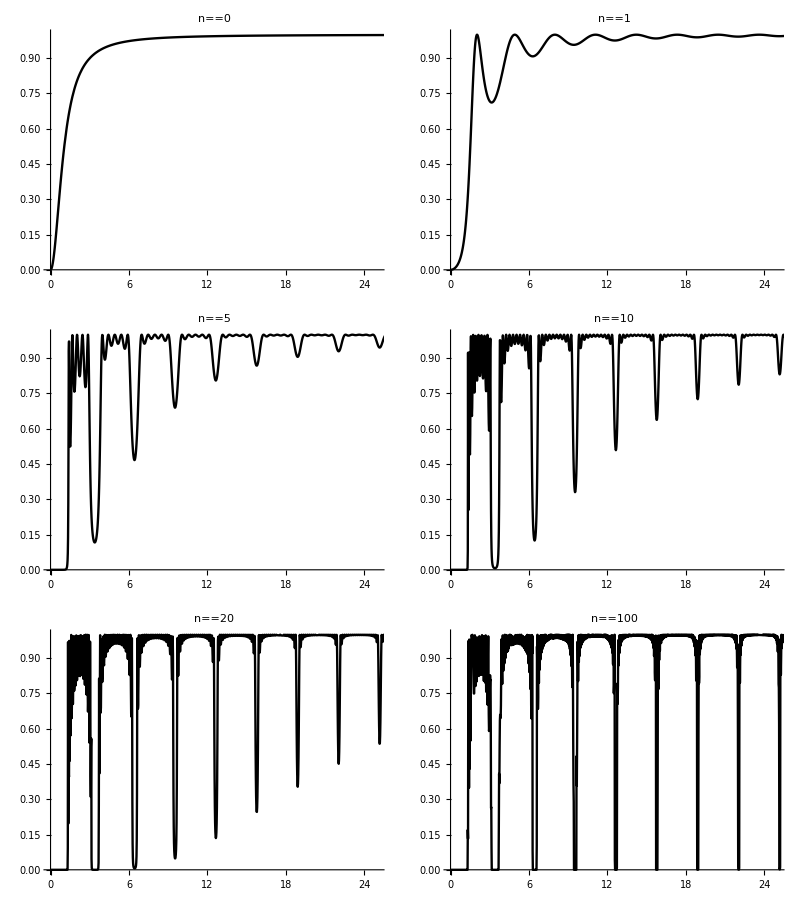

```mathematica
For[w={};i=0,i<6,i++,we=AppendTo[w,ploty[ns[[i+1]]]@wq[ns[[i+1]]]]]
exexe= Grid[{{w[[1]],w[[2]]},{w[[3]],w[[4]]},{w[[5]],w[[6]]}},Dividers->All]
```

```mathematica
Manipulate[Ppl[N]@wq[N],{N,0,5,1}]
```

```mathematica
Manipulate[ListLinePlot[Table[1/(1+((1/k)*Pi*ChebyshevU[n,(-1)^n])^2),{n,0,100,1}],PlotRange->All],{k,36,1200}]
```

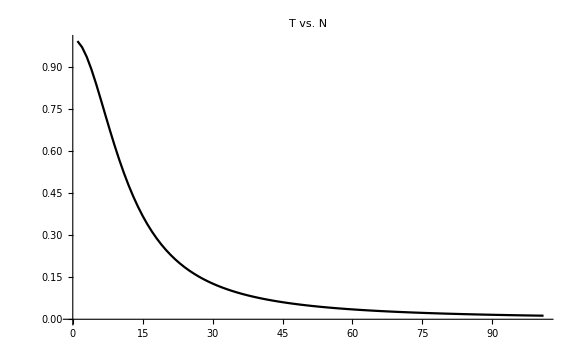

```mathematica
ListLinePlot[Table[1/(1+((1/36)*Pi*ChebyshevU[n,(-1)^n])^2),{n,0,100,1}],PlotRange->All,PlotLabel->"T vs. N",PlotStyle->{Black}]
```

```mathematica
Button["HideInputs",NotebookFind[SelectedNotebook[],"Output",All,CellStyle];
FrontEndExecute[FrontEndToken["OpenCloseGroup"]]]
```

HideInputs